# Evaluating Georgia’s Re-Opening

Georgia has decided to ease many of its COVID-19 restrictions, allowing for many nonessential businesses to reopen. Georgia represents a dilemma held by many states: concern with overwhelming their health care systems and with the economic harms from protective measures. In this notebook, we examine the current state of COVID-19 cases within Georgia and the Southeast region of the U.S. that surrounds Georgia.

TimeConstrained::timc: Number of seconds Predictions`Private`$PITimeConstrained is not a positive machine-sized number or Infinity.

Import["C:\Users\Wilson Bao\Documents\georgiapeach.jpg"]

-Graphics-

## Data Overview

PieChart[{1956558, 955488}, ChartLabels -> {"1,956,558 Cases", "955,488 Cases"}, ChartLegends -> {"Rest of the World", "United States"}]

-Graphics-

Currently, as of April 24, 2020, there are 2,912,046 COVID-19 cases worldwide. The United States consist around 30% of those cases.

PieChart[{880631, 74857}, ChartLabels -> {"880,631 Cases", "74,857 Cases"}, ChartLegends -> {"Rest of United States", "Southeast Region"}]

-Graphics-

The Southeast Region, which includes Georgia, currently has 74,857 COVID-19 cases.

BarChart[{30525, 21575, 8679, 8052, 6026}, ChartLabels -> {"Florida", "Georgia", "Tennessee", "North Carolina", "Alabama"}]

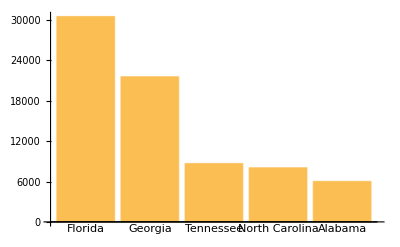

Delving into this region more, Georgia has the second highest number of cases, second to Florida.

Import["C:\Users\Wilson Bao\Documents\Southeastregion.PNG"]

-Graphics-

## Georgian Counties

One way to evaluate Georgia’s reopening is to examine which counties are hit the hardest.

PieChart[{2500, 1721, 1465, 1382, 1368, 1022, 12117}, ChartLabels -> {"2,500 Cases", "1,721 Cases", "1,465 Cases", "1,382 Cases", "1,368 Cases", "1,022 Cases", "12,117 Cases"}, ChartLegends -> {"Tift", "Walton", "Rabun", "Heard", "Bleckley", "Calhoun", "Rest of Georgia"}]

-Graphics-

As seen in the pie chart, 6 of the counties are responsible for almost half of Georgia’s COVID-19 cases.

Import["C:\Users\Wilson Bao\Documents\georgiamap.PNG"]

-Graphics-

Furthermore, these counties are spread throughout the state.

## Forecast Georgia COVID-19 Cases

Import["C:\Users\Wilson Bao\Documents\GeorgiaTSplot.PNG"]

-Graphics-

Georgia COVID-19 cases are trending upwards. As seen in other countries and states, it is likely the trend is an S-Curve: trend will ramp up exponentially with the growth leveling off eventually. Depending on protective measures in place, the growth can grow aggressively or level off (flattening the curve).  Georgia’s trend is still early, and there is large variation in how it can develop.

f[t_] := -855 + 135*t + 10.611*t^2

For forecasting, we used Minitab and developed a quadratic model. We chose this model because there is not enough data for S-Curve. Because we will forecast in the short term, quadratic model fits our purposes. According to our model, each T is 1 day after March 15, 2020. Our data ends on the 41st day, which is April 24, 2020. Therefore, to forecast 15 days, we add the days beyond 41.

{f[42], f[43], f[44], f[45], f[46], f[47], f[48], f[49]}

{23532.8,24569.7,25627.9,26707.3,27807.9,28929.7,30072.7,31237.}

{f[50], f[51], f[52], f[53], f[54], f[55]}

{32422.5,33629.2,34857.1,36106.3,37376.7,38668.3}

F(55) means that on May 9th, 2020, our model forecast Georgia’s COVID-19 cases will be about 38,668.

Import["C:\Users\Wilson Bao\Documents\GeorgiaForecasts.PNG"]

-Graphics-

Here is a graphical representation of these forecasts.

## Forecast Southeast COVID-19 Cases

Import["C:\Users\Wilson Bao\Documents\southtsplot.PNG"]

-Graphics-

Southeast COVID-19 cases are also trending upwards. Southeast region trend also appears to be early on with large variation in how the trend will return out.

f[t_] := -4155 + 742*t + 30.68*t^2

Just as we did for Georgia,  we used Minitab and developed a quadratic model for the same reasons. According to our model, each T is 1 day after March 15, 2020. Our data ends on the 41st day, which is April 24, 2020. Therefore, to forecast 15 days, we add the days beyond 41.

{f[42], f[43], f[44], f[45], f[46], f[47], f[48], f[49]}

{81128.5,84478.3,87889.5,91362.,94895.9,98491.1,102148.,105866.}

{f[50], f[51], f[52], f[53], f[54], f[55]}

{109645.,113486.,117388.,121351.,125376.,129462.}

F(55) means that on May 9th, 2020, our model forecast Georgia’s COVID-19 cases will be about 129,462.

Import["C:\Users\Wilson Bao\Documents\southeastforecast.PNG"]

-Graphics-

Here is a graphical representation of these forecasts.

## Conclusion

In summary, we examined the following: (1) hardest hitting counties in Georgia; (2) forecasts of Georgia COVID-19 cases; and (3) forecasts of Southeast region COVID-19 cases. 
We seen how 6 counties are responsible for almost half of the cases in Georgia. These counties suggest that as Georgia re-opens, state and local governments should carefully consider whether to ease up on previous protective measures. These counties can undo most of the good that the quarantine has done. 

We also see that, if recent growth continue, there will be about 18,000 new cases in Georgia and 55,000 new cases in the entire region.  The forecasts are based on most current data. However, if Georgia reopens, the trend could accelerate not only for its own state, but its neighboring states within the regions as well.